```mathematica
Manipulate[Show[Plot[(12 π)/MZ^2 (s^2 Γi Γf)/((s^2-MZ^2)^2 + s^4 ΓZ^2/ MZ^2)*0.3894/10^-6+U, {s, 80, 100}, PlotRange->All],ListPlot[data]], {{MZ, 91.187}, 80, 100}, {{Γi, 0.084}, 0.05, 0.15, 0.001}, {{Γf, 0.084}, 0.08, 1.8, 0.001}, {{ΓZ, 2.5}, 2, 3, 0.1}, {{U, 0}, 0, 1, 0.01}]
```

{{91.2322,1.89749},{88.4802,0.304981},{89.4716,0.679939},{90.2272,1.24403},{91.9711,1.40468},{92.9709,0.600302},{93.7184,0.394844}}

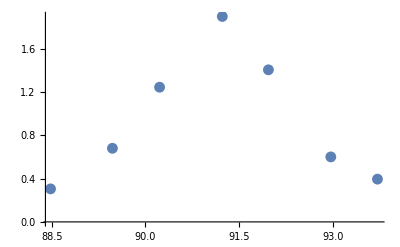

```mathematica
data=Import["/home/moritz/FP2/0427-Z0/calc/crosssections_mm.txt","Table"];
data={#[[1]],#[[2]]}&/@data
ListPlot[data]
```